```mathematica
NicePlot={Frame->True,FrameTicksStyle->{{Directive[20,20],20},{20,20}},FrameStyle->Directive[AbsoluteThickness[0.9],FontFamily->"Helvetica",Black,FontSize->20],AspectRatio->2/3,ImageSize->550};
```

## Plots

```mathematica
y00=SphericalPlot3D[Re[SphericalHarmonicY[0,0,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2π},PlotRange->All,Mesh->False,Axes->False,Boxed->False];
```

```mathematica
y1m1=SphericalPlot3D[Re[SphericalHarmonicY[1,-1,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2π},PlotRange->All,Mesh->False,Axes->False,Boxed->False];
```

```mathematica
y10=SphericalPlot3D[Re[SphericalHarmonicY[1,0,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2π},PlotRange->All,Mesh->False,Axes->False,Boxed->False];
```

```mathematica
y11=SphericalPlot3D[Re[SphericalHarmonicY[1,1,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2π},PlotRange->All,Mesh->False,Axes->False,Boxed->False];
```

```mathematica
y2m2=SphericalPlot3D[Re[SphericalHarmonicY[2,-2,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2π},PlotRange->All,Mesh->False,Axes->False,Boxed->False];
```

```mathematica
y2m1=SphericalPlot3D[Re[SphericalHarmonicY[2,-1,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2π},PlotRange->All,Mesh->False,Axes->False,Boxed->False];
```

```mathematica
y20=SphericalPlot3D[Re[SphericalHarmonicY[2,0,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2π},PlotRange->All,Mesh->False,Axes->False,Boxed->False];
```

```mathematica
y21=SphericalPlot3D[Re[SphericalHarmonicY[2,1,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2π},PlotRange->All,Mesh->False,Axes->False,Boxed->False];
```

```mathematica
y22=SphericalPlot3D[Re[SphericalHarmonicY[2,2,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2π},PlotRange->All,Mesh->False,Axes->False,Boxed->False];
```

```mathematica
GraphicsGrid[{{"","",y00,"",""},{"",y1m1,y10,y11,""},{y2m2,y2m1,y20,y21,y22}},ImageSize->500]
```

-Graphics-

```mathematica
s00=SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},ColorFunction->Function[{x,y,z,θ,ϕ,r},ColorData["DarkRainbow"][6Re[SphericalHarmonicY[0,0,θ,ϕ]]^2]],ColorFunctionScaling->False,Mesh->False,Boxed->False,Axes->False,PlotPoints->50];
```

```mathematica
s1m1=SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},ColorFunction->Function[{x,y,z,θ,ϕ,r},ColorData["DarkRainbow"][6Re[SphericalHarmonicY[1,-1,θ,ϕ]]^2]],ColorFunctionScaling->False,Mesh->False,Boxed->False,Axes->False,PlotPoints->50];
```

```mathematica
s10=SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},ColorFunction->Function[{x,y,z,θ,ϕ,r},ColorData["DarkRainbow"][6Re[SphericalHarmonicY[1,0,θ,ϕ]]^2]],ColorFunctionScaling->False,Mesh->False,Boxed->False,Axes->False,PlotPoints->50];
```

```mathematica
s11=SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},ColorFunction->Function[{x,y,z,θ,ϕ,r},ColorData["DarkRainbow"][6Re[SphericalHarmonicY[1,1,θ,ϕ]]^2]],ColorFunctionScaling->False,Mesh->False,Boxed->False,Axes->False,PlotPoints->50];
```

```mathematica
s2m2=SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},ColorFunction->Function[{x,y,z,θ,ϕ,r},ColorData["DarkRainbow"][6Re[SphericalHarmonicY[2,-2,θ,ϕ]]^2]],ColorFunctionScaling->False,Mesh->False,Boxed->False,Axes->False,PlotPoints->50];
```

```mathematica
s2m1=SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},ColorFunction->Function[{x,y,z,θ,ϕ,r},ColorData["DarkRainbow"][6Re[SphericalHarmonicY[2,-1,θ,ϕ]]^2]],ColorFunctionScaling->False,Mesh->False,Boxed->False,Axes->False,PlotPoints->50];
```

```mathematica
s20=SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},ColorFunction->Function[{x,y,z,θ,ϕ,r},ColorData["DarkRainbow"][6Re[SphericalHarmonicY[2,0,θ,ϕ]]^2]],ColorFunctionScaling->False,Mesh->False,Boxed->False,Axes->False,PlotPoints->50];
```

```mathematica
s21=SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},ColorFunction->Function[{x,y,z,θ,ϕ,r},ColorData["DarkRainbow"][6Re[SphericalHarmonicY[2,1,θ,ϕ]]^2]],ColorFunctionScaling->False,Mesh->False,Boxed->False,Axes->False,PlotPoints->50];
```

```mathematica
s22=SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},ColorFunction->Function[{x,y,z,θ,ϕ,r},ColorData["DarkRainbow"][6Re[SphericalHarmonicY[2,2,θ,ϕ]]^2]],ColorFunctionScaling->False,Mesh->False,Boxed->False,Axes->False,PlotPoints->50];
```

```mathematica
GraphicsGrid[{{"","",s00,"",""},{"",s1m1,s10,s11,""},{s2m2,s2m1,s20,s21,s22}},ImageSize->500]
```

-Graphics-

```mathematica
elevels=Table[{l,BesselJZero[l+1/2,n+1]^2//N},{l,0,3},{n,0,5}]~Flatten~1
```

{{0,9.8696},{0,39.4784},{0,88.8264},{0,157.914},{0,246.74},{0,355.306},{1,20.1907},{1,59.6795},{1,118.9},{1,197.858},{1,296.554},{1,414.99},{2,33.2175},{2,82.7192},{2,151.855},{2,240.703},{2,349.28},{2,477.592},{3,48.8312},{3,108.516},{3,187.636},{3,286.409},{3,404.887},{3,543.088}}

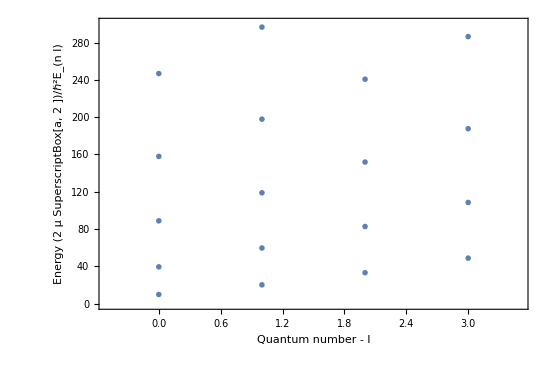

```mathematica
Show[ListPlot[elevels,PlotRange->{{-0.5,3.5},{0,300}},PlotMarkers->{"---",Large},Frame->True, Axes->False,FrameLabel->{"Quantum number - l","Energy (2  μ SuperscriptBox[a, 2 ])/ℏ^2E_(n l)"}],NicePlot]
```

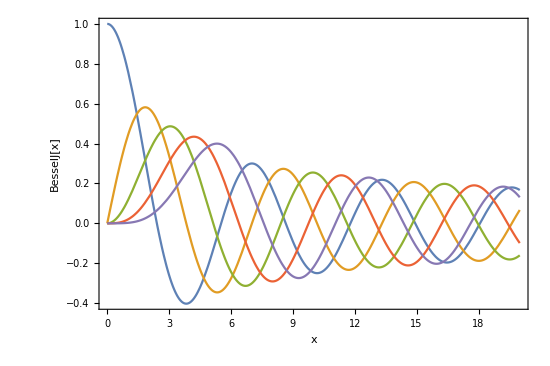

```mathematica
Show[Plot[{BesselJ[0,x],BesselJ[,x],BesselJ[2,x],BesselJ[3,x],BesselJ[4,x]},{x,0,20},PlotRange->All,FrameLabel->{"x","BesselJ[x]"}],NicePlot]
```

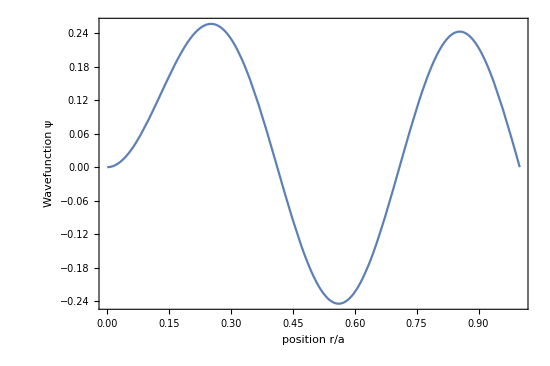

```mathematica
Show[With[{l=1,n=2},Plot[√r BesselJ[l+1/2,r BesselJZero[l+1/2,n+1]],{r,0,1},ImageSize->500, Frame->True, FrameLabel->{"position r/a","Wavefunction ψ"}]],NicePlot]
```

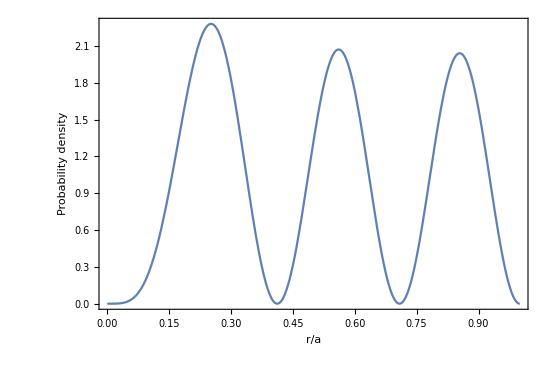

```mathematica
Module[{l=1,n=2,norm},norm=NIntegrate[(√r BesselJ[l+1/2,r BesselJZero[l+1/2,n+1]])^2,{r,0,1}];Show[Plot[(√r BesselJ[l+1/2,r BesselJZero[l+1/2,n+1]])^2/norm,{r,0,1},PlotRange->All,Frame->True,Axes->False, FrameLabel->{"r/a","Probability density"}],NicePlot]]
```

```mathematica
Bzeros=Table[N[BesselJZero[l+1/2,n+1]],{n,0,5,1},{l,0,5,1}];
```

```mathematica
Manipulate[With[{r=√(x^2+z^2),θ=ArcCos[z/(√(x^2+z^2))]},ContourPlot[If[r>1,0,(√r BesselJ[l+1/2,r *Bzeros⟦n+1,l+1⟧ ])^2/r^2 Abs[SphericalHarmonicY[l,m,θ,0]]^2],{x,-1,1},{z,-1,1},PlotRange->{0,.2},Contours->20,ColorFunction->ColorData["GrayYellowTones"],ImageSize->500,Frame->True,Axes->False, FrameLabel->{"x","z"}]],{n,0,3,1},{l,0,3,1},{m,0,3,1}]
```

```mathematica
timeSave=N[BesselJZero[2+1/2,2+1]]
```

12.3229

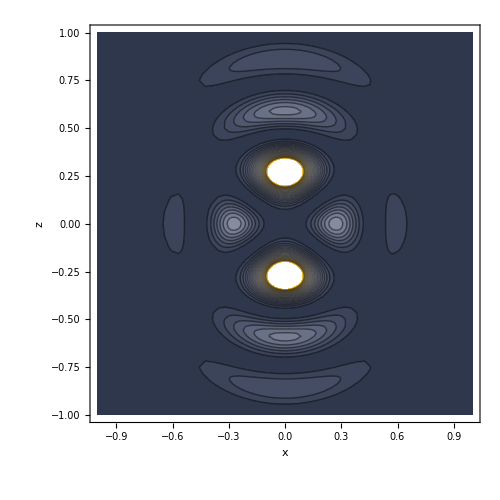

```mathematica
With[{l=2,m=0,n=2,r=√(x^2+z^2),θ=ArcCos[z/(√(x^2+z^2))]},ContourPlot[If[r>1,0,(√r BesselJ[l+1/2,r timeSave])^2/r^2 Abs[SphericalHarmonicY[l,m,θ,0]]^2],{x,-1,1},{z,-1,1},PlotRange->{0,.2},Contours->20,ColorFunction->ColorData["GrayYellowTones"],ImageSize->500,Frame->True,Axes->False, FrameLabel->{"x","z"}]]
```